```mathematica
Get["~/Nutstore/On Thinking/Non-Gaussianity/Programmes/Data Saved/Saved/resultOfExpansion.txt"];
```

Import packages:

```mathematica
path = "~/Nutstore/On Thinking/Git/Tools-For-QFT/Package_NG/";

Get[path<>"Basics/BasicAlgebraicOperations/OperationsOnVariables.m"]
Get[path<>"Basics/BasicAlgebraicOperations/DivideLongSummation.m"]
Get[path<>"Basics/BasicAlgebraicOperations/seperateMultipliedSubExprsAsList.m"]
Get[path<>"Basics/BasicAlgebraicOperations/ProtectSymbols.m"]
Get[path<>"Basics/BasicAlgebraicOperations/DivideLongSummation.m"]
Get[path<>"Basics/fourierTransformAdv/replaceByFourierExpansion_integrateAdv.m"]
Get[path<>"Basics/fourierTransformAdv/basicRulesForIntegrateAdv.m"]
Get[path<>"Basics/actOn/ActOn.m"]
```

```mathematica
Timing[list3OrderPert = divideLongSummationIntoList[Expand@resultOfExpansion3Ord];]
```

{0.577912,Null}

```mathematica
Length@list3OrderPert
```

823

```mathematica
list3OrderPert[[100]]
```

-6 a[t] ℛ[x,y,z,t]^2 ℛ^(0,0,2,0)[x,y,z,t]

```mathematica
seperateMultipliedSubExprsAsList@list3OrderPert[[100]]
```

{-1,6,a[t],ℛ[x,y,z,t],ℛ[x,y,z,t],ℛ^(0,0,2,0)[x,y,z,t]}

```mathematica
Timing[tmp1 = replaceByFourierExpansion[list3OrderPert[[100]], {ℛ, ζ}]]
```

{0.001,{-1,6,a[t],integrateAdv[ⅇ^(ⅈ (k1$673 x+k2$674 y+k3$675 z)) ζ[k1$673,k2$674,k3$675,t],{{k1$673,-∞,∞},{k2$674,-∞,∞},{k3$675,-∞,∞}},{}],integrateAdv[ⅇ^(ⅈ (k1$677 x+k2$678 y+k3$679 z)) ζ[k1$677,k2$678,k3$679,t],{{k1$677,-∞,∞},{k2$678,-∞,∞},{k3$679,-∞,∞}},{}],integrateAdv[-ⅇ^(ⅈ (k1$681 x+k2$682 y+k3$683 z)) k3$683^2 ζ[k1$681,k2$682,k3$683,t],{{k1$681,-∞,∞},{k2$682,-∞,∞},{k3$683,-∞,∞}},{}]}}

```mathematica
Timing[tmp2 = tmp1/.{ζ[k1_, k2_, k3_, t_] -> u[k1, k2, k3, t] aOpt[k1, k2, k3] + uStar[-k1, -k2, -k3, t] dagger@aOpt[-k1, -k2, -k3]}]
```

{0.,{-1,6,a[t],integrateAdv[ⅇ^(ⅈ (k1$673 x+k2$674 y+k3$675 z)) (aOpt[k1$673,k2$674,k3$675] u[k1$673,k2$674,k3$675,t]+dagger[aOpt[-k1$673,-k2$674,-k3$675]] uStar[-k1$673,-k2$674,-k3$675,t]),{{k1$673,-∞,∞},{k2$674,-∞,∞},{k3$675,-∞,∞}},{}],integrateAdv[ⅇ^(ⅈ (k1$677 x+k2$678 y+k3$679 z)) (aOpt[k1$677,k2$678,k3$679] u[k1$677,k2$678,k3$679,t]+dagger[aOpt[-k1$677,-k2$678,-k3$679]] uStar[-k1$677,-k2$678,-k3$679,t]),{{k1$677,-∞,∞},{k2$678,-∞,∞},{k3$679,-∞,∞}},{}],integrateAdv[-ⅇ^(ⅈ (k1$681 x+k2$682 y+k3$683 z)) k3$683^2 (aOpt[k1$681,k2$682,k3$683] u[k1$681,k2$682,k3$683,t]+dagger[aOpt[-k1$681,-k2$682,-k3$683]] uStar[-k1$681,-k2$682,-k3$683,t]),{{k1$681,-∞,∞},{k2$682,-∞,∞},{k3$683,-∞,∞}},{}]}}

```mathematica
FundamentalQNumbers = {{aOpt, boson}};
```

```mathematica
tmp2[[4]]
```

integrateAdv[ⅇ^(ⅈ (k1$673 x+k2$674 y+k3$675 z)) (aOpt[k1$673,k2$674,k3$675] u[k1$673,k2$674,k3$675,t]+dagger[aOpt[-k1$673,-k2$674,-k3$675]] uStar[-k1$673,-k2$674,-k3$675,t]),{{k1$673,-∞,∞},{k2$674,-∞,∞},{k3$675,-∞,∞}},{}]

```mathematica
Timing[tmpResult1 = actOn[tmp2[[4]], ket[{}]]]
```

{0.008999,integrateAdv[ⅇ^(ⅈ (k1$673 x+k2$674 y+k3$675 z)) ket[{aOpt[-k1$673,-k2$674,-k3$675]}] uStar[-k1$673,-k2$674,-k3$675,t],{{k1$673,-∞,∞},{k2$674,-∞,∞},{k3$675,-∞,∞}},{}]}

Wonderful!!!

```mathematica
tmp3 = Times@@tmp2
```

-6 a[t] integrateAdv[ⅇ^(ⅈ (k1$673 x+k2$674 y+k3$675 z)) (aOpt[k1$673,k2$674,k3$675] u[k1$673,k2$674,k3$675,t]+dagger[aOpt[-k1$673,-k2$674,-k3$675]] uStar[-k1$673,-k2$674,-k3$675,t]),{{k1$673,-∞,∞},{k2$674,-∞,∞},{k3$675,-∞,∞}},{}] integrateAdv[ⅇ^(ⅈ (k1$677 x+k2$678 y+k3$679 z)) (aOpt[k1$677,k2$678,k3$679] u[k1$677,k2$678,k3$679,t]+dagger[aOpt[-k1$677,-k2$678,-k3$679]] uStar[-k1$677,-k2$678,-k3$679,t]),{{k1$677,-∞,∞},{k2$678,-∞,∞},{k3$679,-∞,∞}},{}] integrateAdv[-ⅇ^(ⅈ (k1$681 x+k2$682 y+k3$683 z)) k3$683^2 (aOpt[k1$681,k2$682,k3$683] u[k1$681,k2$682,k3$683,t]+dagger[aOpt[-k1$681,-k2$682,-k3$683]] uStar[-k1$681,-k2$682,-k3$683,t]),{{k1$681,-∞,∞},{k2$682,-∞,∞},{k3$683,-∞,∞}},{}]

```mathematica
tmp31 = Times[a[t], tmp2[[4]], tmp2[[5]]]
```

a[t] integrateAdv[ⅇ^(ⅈ (k1$673 x+k2$674 y+k3$675 z)) (aOpt[k1$673,k2$674,k3$675] u[k1$673,k2$674,k3$675,t]+dagger[aOpt[-k1$673,-k2$674,-k3$675]] uStar[-k1$673,-k2$674,-k3$675,t]),{{k1$673,-∞,∞},{k2$674,-∞,∞},{k3$675,-∞,∞}},{}] integrateAdv[ⅇ^(ⅈ (k1$677 x+k2$678 y+k3$679 z)) (aOpt[k1$677,k2$678,k3$679] u[k1$677,k2$678,k3$679,t]+dagger[aOpt[-k1$677,-k2$678,-k3$679]] uStar[-k1$677,-k2$678,-k3$679,t]),{{k1$677,-∞,∞},{k2$678,-∞,∞},{k3$679,-∞,∞}},{}]

```mathematica
Timing[actOn[(ⅇ^(ⅈ (k1$2784 x+k2$2785 y+k3$2786 z)) (aOpt[k1$2784,k2$2785,k3$2786] u[k1$2784,k2$2785,k3$2786,t]+dagger[aOpt[-k1$2784,-k2$2785,-k3$2786]] uStar[-k1$2784,-k2$2785,-k3$2786,t]))*(ⅇ^(ⅈ (k1$618 x+k2$619 y+k3$620 z)) (aOpt[k1$618,k2$619,k3$620] u[k1$618,k2$619,k3$620,t]+dagger[aOpt[-k1$618,-k2$619,-k3$620]] uStar[-k1$618,-k2$619,-k3$620,t])), ket[{}]]]
```

{0.015998,ⅇ^(ⅈ (k1$2784 x+k2$2785 y+k3$2786 z)+ⅈ (k1$618 x+k2$619 y+k3$620 z)) (DiracDelta[k1$2784+k1$618] DiracDelta[k2$2785+k2$619] DiracDelta[k3$2786+k3$620] ket[{}] u[k1$2784,k2$2785,k3$2786,t] uStar[-k1$618,-k2$619,-k3$620,t]+ket[{aOpt[-k1$618,-k2$619,-k3$620],aOpt[-k1$2784,-k2$2785,-k3$2786]}] uStar[-k1$2784,-k2$2785,-k3$2786,t] uStar[-k1$618,-k2$619,-k3$620,t])}

You see, if get rid of the integrals, or if not evaluate the integrals, the programme is quite quite wonderful, otherwise, because of the horrible but useless evaluation of those integrals, this progamme becomes useless!!!

So, all the reason making the programme slow or even become useless is that Mathematica always keeps evaluating the integrals within the procedure, which is useless and useless until the end of the whole procedure!!!

======================= Debugs Below =======================

```mathematica
ClearAll[pureActOn]
```

```mathematica
Timing[tmp4 = actOn[tmp31, ket[{}]]]
```

$Aborted

```mathematica
tmp21 = tmp2[[4]]*tmp2[[5]]
```

(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$176 x+k2$177 y+k3$178 z)) (a[k1$176,k2$177,k3$178] u[k1$176,k2$177,k3$178,t]+dagger[a[-k1$176,-k2$177,-k3$178]] uStar[-k1$176,-k2$177,-k3$178,t])ⅆk3$178ⅆk2$177ⅆk1$176) ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) (a[k1$2356,k2$2357,k3$2358] u[k1$2356,k2$2357,k3$2358,t]+dagger[a[-k1$2356,-k2$2357,-k3$2358]] uStar[-k1$2356,-k2$2357,-k3$2358,t])ⅆk3$2358ⅆk2$2357ⅆk1$2356

```mathematica
Length@tmp2
```

6

```mathematica
Timing[actOn[]]
```

```mathematica
f1 = actOn[tmp2[[6]], ket[{}]]
```

-∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$4445 x+k2$4446 y+k3$4447 z)) k3$4447^2 ket[{a[-k1$4445,-k2$4446,-k3$4447]}] uStar[-k1$4445,-k2$4446,-k3$4447,t]ⅆk3$4447ⅆk2$4446ⅆk1$4445

```mathematica
actOn[tmp2[[5]], f1]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ Null\ Integrate`ImproperDump`res$51979\ ∞ encountered.

Infinity::indet: Indeterminate expression 0\ ∞\ (Integrate`ImproperDump`res$51984/. Hold[Hold[Hold[Hold[Hold[« 1 »]]]] → Solve`RootsAuxVar]) encountered.

$Aborted

```mathematica
Timing[tmp221 = pureActOn[a[p1,p2,p3], actOn[tmp2[[5]], ket[{}]]]]
```

{5.00224,ConditionalExpression[ⅇ^(-ⅈ (p1 x+p2 y+p3 z)) ket[{}] uStar[p1,p2,p3,t],p1∈Reals]}

```mathematica
f1
```

-∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$4445 x+k2$4446 y+k3$4447 z)) k3$4447^2 ket[{a[-k1$4445,-k2$4446,-k3$4447]}] uStar[-k1$4445,-k2$4446,-k3$4447,t]ⅆk3$4447ⅆk2$4446ⅆk1$4445

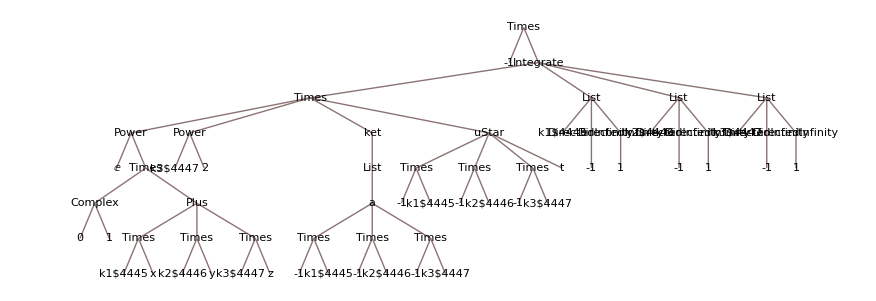

```mathematica
TreeForm@f1
```

```mathematica
ClearAll[pureActOn]
```

```mathematica
Timing[tmp221 = actOn[a[p1,p2,p3], ⅇ^(ⅈ (k1$4445 x+k2$4446 y+k3$4447 z)) k3$4447^2 ket[{a[-k1$4445,-k2$4446,-k3$4447]}] uStar[-k1$4445,-k2$4446,-k3$4447,t]]]
```

{0.001999,ⅇ^(ⅈ (k1$4445 x+k2$4446 y+k3$4447 z)) k3$4447^2 DiracDelta[k1$4445+p1] DiracDelta[k2$4446+p2] DiracDelta[k3$4447+p3] ket[{}] uStar[-k1$4445,-k2$4446,-k3$4447,t]}

```mathematica
actOn[a[p1,p2,p3], ket[{a[-k1$4445,-k2$4446,-k3$4447]}]*uStar[-k1$4445,-k2$4446,-k3$4447,t]]
```

DiracDelta[k1$4445+p1] DiracDelta[k2$4446+p2] DiracDelta[k3$4447+p3] ket[{}] uStar[-k1$4445,-k2$4446,-k3$4447,t]

```mathematica
Timing[actOn[a[p1,p2,p3], f1]]
```

{0.936858,ConditionalExpression[-ⅇ^(-ⅈ (p1 x+p2 y+p3 z)) p3^2 ket[{}] uStar[p1,p2,p3,t],p1∈Reals]}

```mathematica
Timing[tmp22 = actOn[tmp21, ket[{}]]]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

{4.71228,∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$176 x+k2$177 y+k3$178 z)) ((∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫Hold[Integrate[pureActOn[a[k1$176,k2$177,k3$178],∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356/.{∫Integrand_ⅆVariable_→Integrand}],∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356/.{∫Integrand_ⅆVariable_→Variable}]]ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356)) u[k1$176,k2$177,k3$178,t]+(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫(∫Hold[Integrate[pureActOn[dagger[a[-k1$176,-k2$177,-k3$178]],∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356/.{∫Integrand_ⅆVariable_→Integrand}],∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356/.{∫Integrand_ⅆVariable_→Variable}]]ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356))ⅆ(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(ⅈ (k1$2356 x+k2$2357 y+k3$2358 z)) ket[{a[-k1$2356,-k2$2357,-k3$2358]}] uStar[-k1$2356,-k2$2357,-k3$2358,t]ⅆk3$2358ⅆk2$2357ⅆk1$2356)) uStar[-k1$176,-k2$177,-k3$178,t])ⅆk3$178ⅆk2$177ⅆk1$176}

That means if the state acted on is complex, the result will be missable!!!

So, next, we shall handle with the pureActOn[], within which the procedure of simplification must be wrong, I GUESS~~

```mathematica
Timing[tmp4 = actOn[tmp3, ket[{}]]]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Set::write: Tag ReplaceAll in integrateAdv[-ⅇ^ⅈ\ (k1$681\ x + k2$682\ y + k3$683\ z)\ k3$683^2\ ket[{aOpt[-k1$681, -k2$682, -k3$683]}]\ uStar[-k1$681, -k2$682, -k3$683, t], {{k1$681, -∞, ∞}, {k2$682, -∞, ∞}, {k3$683, -∞, ∞}}, {}]/. {result$1960\ (integrateAdv[Integrand0$_, VariablesList0$_, Rules0$1960] → Rules0$1960)} is Protected.

Set::write: Tag ReplaceAll in integrateAdv[-ⅇ^ⅈ\ (k1$681\ x + k2$682\ y + k3$683\ z)\ k3$683^2\ ket[{aOpt[-k1$681, -k2$682, -k3$683]}]\ uStar[-k1$681, -k2$682, -k3$683, t], {{k1$681, -∞, ∞}, {k2$682, -∞, ∞}, {k3$683, -∞, ∞}}, {}]/. {result$1958\ (integrateAdv[Integrand0$_, VariablesList0$_, Rules0$1958] → Rules0$1958)} is Protected.

Set::write: Tag ReplaceAll in integrateAdv[-ⅇ^ⅈ\ (k1$681\ x + k2$682\ y + k3$683\ z)\ k3$683^2\ ket[{aOpt[-k1$681, -k2$682, -k3$683]}]\ uStar[-k1$681, -k2$682, -k3$683, t], {{k1$681, -∞, ∞}, {k2$682, -∞, ∞}, {k3$683, -∞, ∞}}, {}]/. {result$1956\ (integrateAdv[Integrand0$_, VariablesList0$_, Rules0$1956] → Rules0$1956)} is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

{0.157975,-6 a[t] integrateAdv[ⅇ^(ⅈ (k1$673 x+k2$674 y+k3$675 z)) (result$2233 u[k1$673,k2$674,k3$675,t]+result$2350 uStar[-k1$673,-k2$674,-k3$675,t]),{{k1$673,-∞,∞},{k2$674,-∞,∞},{k3$675,-∞,∞}},{}]}